# Animated Riemann

## This Mathematica notebook is an extension of the work in the notebook RiemannSums.nb posted in the of abstractmath.org. It is produced by and is licensed under a , which makes it freely available for others to use, provided they refer to this file.

## Riemann Package version 2

This package provides PlotRiemann, which shows Riemann sum of a given integral with various choices of parameters, and CloudList, which plots the values of a number of random Riemann sums of the given integral.  It is a work in progress. You are encouraged to improve this work and to use it in your own publications and coursework.

```mathematica
SetOptions[Plot,AspectRatio->Automatic];
```

```mathematica
PlotBounded[expression_,range_,options___]:=Module[{g,f,left,right,newleft,newright,var,leftheight,rightheight,width,newrange},var=range[[1]];
f=Function[Release[var],expression];
left=range[[2]];
right=range[[3]];
width=right-left;
leftheight=f[left];
rightheight=f[right];
newleft=left-0.25*width;
newright=right+0.25*width;
newrange={var,newleft,newright};
g:=Plot[expression,Release[newrange],DisplayFunction->Identity,PlotStyle->{{RGBColor[0,0,1]}},options];
Show[g,Graphics[{Line[{{left,0},{left,leftheight}}],Line[{{right,0},{right,rightheight}}]}],DisplayFunction->$DisplayFunction]]
```

```mathematica
RandomPartition[range_,mesh_]:=Module[{u=range[[2]],top=range[[3]],list={range[[2]]},v,newlist,actualmesh=0},While[u+mesh<top,v=u+Random[Real,mesh];
actualmesh=Max[actualmesh,v-u];
newlist:=Append[list,v];
u=v;
list=newlist];
partitionstring=StringJoin["Random partition with maximum norm ",ToString[mesh]];
actualmesh=Max[actualmesh,top-Last[list]];
Return[{Append[list,top],actualmesh}]]
```

```mathematica
UniformPartition[range_,number_]:=Module[{bottom=range[[2]]//N,top=range[[3]]//N,actualmesh},actualmesh=(top-bottom)/number;
partitionstring=StringJoin["Uniform partition into ",ToString[number]," subintervals"];
Return[{N[Range[bottom,top,actualmesh]],actualmesh}]]
```

```mathematica
Slices[expression_,variable_,list_,options___Rule]:=Module[{i=1,startlist=list,leftlist,rightlist,widthlist,selectlist,arealist,heightlist,valuelist,opt=Height/.{options}/.Options[RiemannData],f=Function[variable,expression]},leftlist=Drop[list,-1];
rightlist=Drop[list,1];
widthlist=rightlist-leftlist;
selectlist=Switch[opt,LeftSide,(heightstring="Left edge of subinterval used for height";leftlist),RightSide,(heightstring="Right edge of subinterval used for height";rightlist),Midpoint,(heightstring="Midpoint of subinterval used for height";
leftlist+0.5*widthlist),Random,(heightstring="Random point in subinterval used for height";
leftlist+(Random[Real,#]&/@widthlist))];
heightlist=f/@selectlist;
arealist=heightlist*widthlist;
{heightlist,arealist}]
```

```mathematica
(*Boxx::usage="Boxx[bottom, top, left, right]
produces a series of Line statements which in a
Graphics object will draw a hollow rectangle with
the corners given.  (Note that the built in
command Rectangle draws a solid rectangle.)"*)
```

```mathematica
Boxx[bottom_,top_,left_,right_]:=Line[{{left,bottom},{right,bottom},{right,top},{left,top},{left,bottom}}]
```

```mathematica
ShowSlices[partition_,heightlist_]:=Table[Boxx[0,heightlist[[i]],partition[[i]],partition[[i+1]]],{i,1,Length[partition]-1}]
```

```mathematica
Options[RiemannData]:={Subintervals->12,Partition->Uniform,Mesh->intervallength/6.0,Height->Midpoint}
```

```mathematica
RiemannData[expression_, range_, options___Rule] :=
	Block[{M=Mesh /. {options} 
			/. Options[RiemannData],
		S=Subintervals /. {options} 
			/. Options[RiemannData],
		P=Partition /. {options} 
			/. Options[RiemannData],
		variable=range[[1]],
		intervallength=range[[3]]-range[[2]]},
		list=Switch[P, Uniform, 
			UniformPartition[range, S],
			Random,
			RandomPartition[range, M]
           ]; 
	{list[[1]]} ~Join~ 
		Slices[expression, variable, list[[1]], options]
		~Join~ {list[[2]]}]
```

```mathematica
RiemannSum[expression_,range_,options___Rule]:=Apply[Plus,RiemannData[expression,range,options][[3]]]
```

```mathematica
PlotRiemann[expression_,range_,{plotoptions___},{riemannoptions___}]:=
Block[
{g,u,partition,heightlist,sum,mesh,integralvalue,outstring},(u=RiemannData[expression,range,riemannoptions
];
partition=u[[1]];
heightlist=u[[2]];
sum=Apply[Plus,u[[3]]];
mesh=u[[4]];
integralvalue=NIntegrate[expression,range];
outstring=StringJoin[
"\n",
"Function: ", 
ToString[TraditionalForm[expression]],
"\n",
partitionstring,
"\n",
heightstring,
"\n",
"Riemann Sum = ",
ToString[Chop[sum]],
"    ",
"Definite Integral = ",
ToString[integralvalue],
"\n",
"Norm = ",
ToString[mesh],
"    ",
"Percent error =",
ToString[
NumberForm[
Chop[Abs[100*(integralvalue-sum)/integralvalue]],
3]
]
];
g:=Plot[expression,range,DisplayFunction->Identity,PlotLabel->outstring,PlotStyle->{{RGBColor[0,0,1]}},plotoptions];
h:=Graphics[{RGBColor[.8,.3,0],ShowSlices[partition,heightlist]}];
Show[g,h,DisplayFunction->$DisplayFunction])]
```

```mathematica
PlotRiemann[expression_,range_]:=PlotRiemann[expression,range,{},{}];
```

## CloudList

### Code

```mathematica
(*RandomCloudList{e, i,n] produces n points(m, riemann sum of expression e on the interval i), where the Riemann Sum has random mesh m with random choice of points in each subinterval.*)
```

```mathematica
RandomCloudList[expression_,range_,n_]:=Module[{l={},s,mesh,a,b,u},a=range[[2]];b=range[[3]];
Do[(mesh=Random[Real,{0,(b-a)/2}];
u=RiemannData[expression,range,Partition->Random,Mesh->mesh,Height->Random];
s=Apply[Plus,u[[3]]];
l=Append[l,{u[[4]],s}]),{i,1,n}];
l]
```

```mathematica
MidpointCloudList[expression_, range_, n_] := Module[{l = {}, s, mesh, a, b, u}, a = range[[2]]; b = range[[3]];
  Do[(mesh=Random[Real,{0,(b-a)/2}];
    u = RiemannData[expression, range, Partition -> Random, Mesh->mesh, Height -> Midpoint]; 
    s = Apply[Plus, u[[3]]];
    l = Append[l, {u[[4]], s}]), {i, 1, n}];
  l]
```

```mathematica
LeftSideCloudList[expression_, range_, n_] := Module[{l = {}, s, mesh, a, b, u}, a = range[[2]]; b = range[[3]];
  Do[(mesh=Random[Real,{0,(b-a)/2}];
    u = RiemannData[expression, range, Partition -> Random, Mesh->mesh, Height -> LeftSide]; 
    s = Apply[Plus, u[[3]]];
    l = Append[l, {u[[4]], s}]), {i, 1, n}];
  l]
```

```mathematica
RightSideCloudList[expression_, range_, n_] := Module[{l = {}, s, mesh, a, b, u}, a = range[[2]]; b = range[[3]];
  Do[(mesh=Random[Real,{0,(b-a)/2}];
    u = RiemannData[expression, range, Partition -> Random, Mesh->mesh, Height -> RightSide]; 
    s = Apply[Plus, u[[3]]];
    l = Append[l, {u[[4]], s}]), {i, 1, n}];
  l]
```

### Examples

```mathematica
Manipulate[
PlotRiemann[
Sin[Pi x],{x,0,1},{ImageSize->Medium,
AspectRatio->1/Pi},
{Partition -> Random,Height -> Random,Mesh->intervallength/n//N}],{{n,12},1,100,1},SaveDefinitions->True]
```

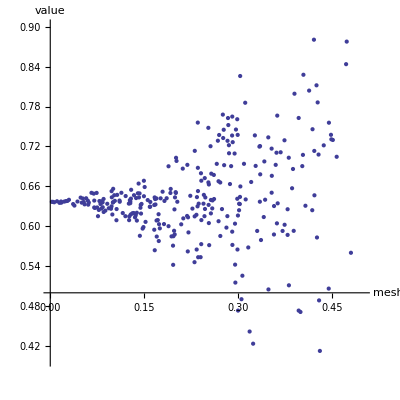

```mathematica
ListPlot[RandomCloudList[Sin[Pi x],{x,0,1},300],AxesLabel->{"mesh","value"},PlotRange->{{0,.5},{.4,.9}},Axes->True,AxesOrigin->{0,.5},AspectRatio->1,PlotRangeClipping->False]
```

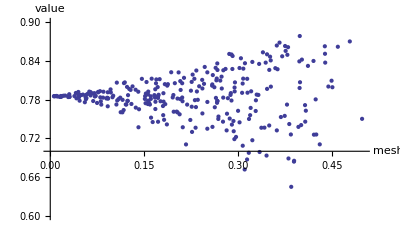

```mathematica
ListPlot[RandomCloudList[Sqrt[1-x^2],{x,0,1},300],Axes->True,AxesOrigin->{0,.7},AxesLabel->{"mesh","value"},PlotRange->{{0,.5},{.6,.9}},AspectRatio->3/5,PlotRangeClipping->False]
```

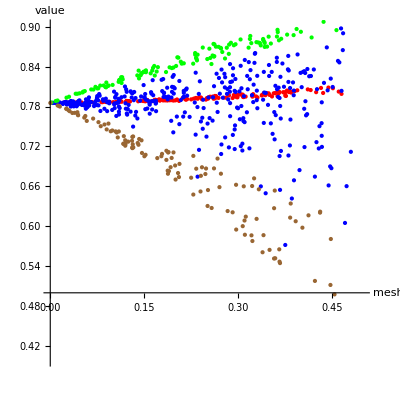

```mathematica
circle[x_]:=Sqrt[1-x^2];
ListPlot[
{
MidpointCloudList[circle[x],{x,0,1},150],
RandomCloudList[circle[x],{x,0,1},350],
LeftSideCloudList[circle[x],{x,0,1},120],
RightSideCloudList[circle[x],{x,0,1},120]
},
PlotStyle->{Red,Blue, Green, Brown},
AxesLabel->{"mesh","value"},
PlotRange->{{0,.5},{.4,.9}},
Axes->True,AxesOrigin->{0,.5},
AspectRatio->1,
PlotRangeClipping->False
]
```

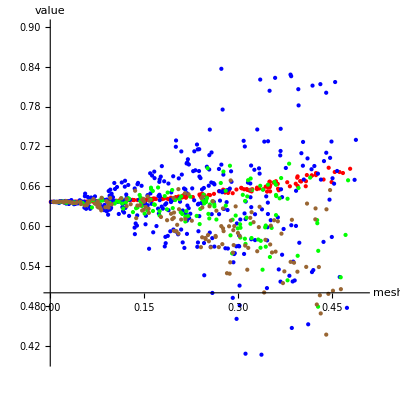

```mathematica
sine[x_]:=Sin[Pi x];
ListPlot[
{
MidpointCloudList[sine[x],{x,0,1},150],
RandomCloudList[sine[x],{x,0,1},350],
LeftSideCloudList[sine[x],{x,0,1},150],
RightSideCloudList[sine[x],{x,0,1},150]
},
PlotStyle->{Red,Blue, Green, Brown},
AxesLabel->{"mesh","value"},
PlotRange->{{0,.5},{.4,.9}},
Axes->True,
AxesOrigin->{0,.5},
AspectRatio->1,
PlotRangeClipping->False
]
```

```mathematica
circlelist=(circle[x_]:=Sqrt[1-x^2];
ListPlot[
{
MidpointCloudList[circle[x],{x,0,1},150],
RandomCloudList[circle[x],{x,0,1},350],
LeftSideCloudList[circle[x],{x,0,1},120],
RightSideCloudList[circle[x],{x,0,1},120]
},
PlotStyle->{Red,Blue, Green, Brown},
AxesLabel->{"mesh","value"},
PlotRange->{{0,.5},{.4,.9}},
Axes->True,AxesOrigin->{0,.5},
AspectRatio->1,
PlotRangeClipping->False
]& /@ Range[1,200])
```

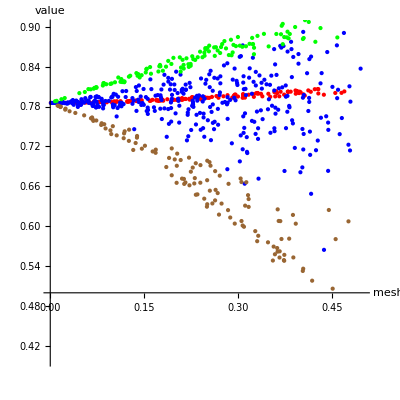
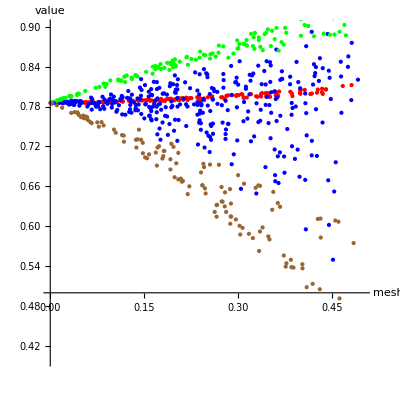
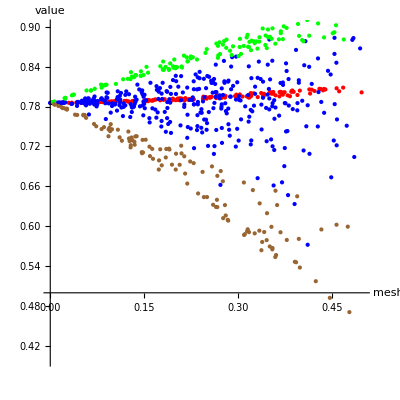
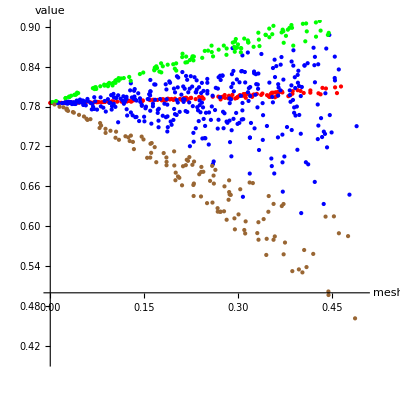
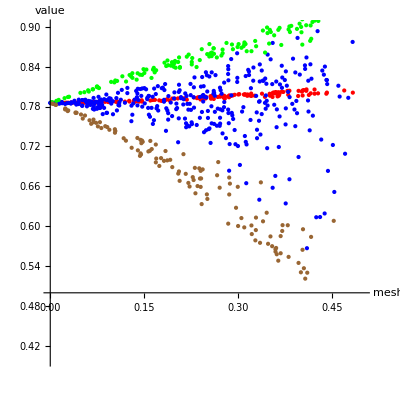
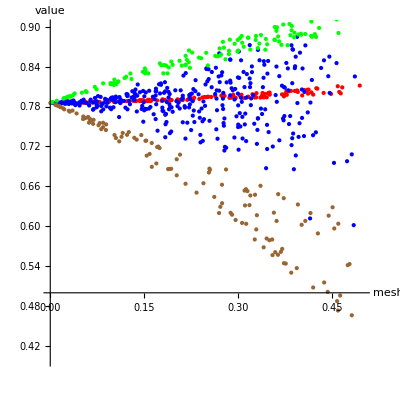
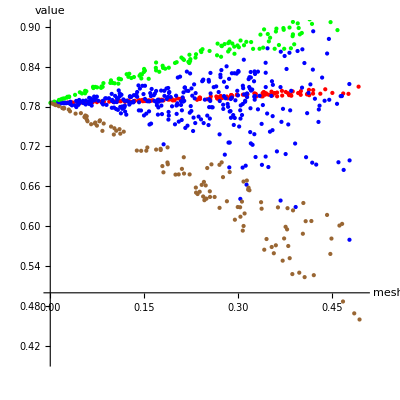
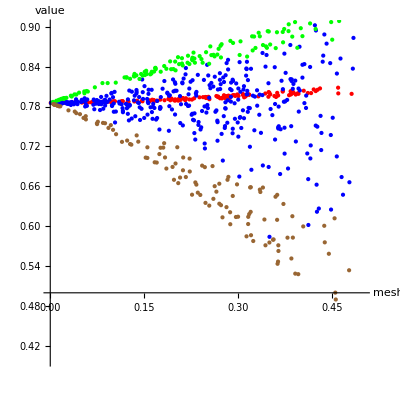
```mathematica
circlecloud={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
sinelist=(sine[x_]:=Sin[Pi x];
ListPlot[
{
MidpointCloudList[sine[x],{x,0,1},150],
RandomCloudList[sine[x],{x,0,1},350],
LeftSideCloudList[sine[x],{x,0,1},150],
RightSideCloudList[sine[x],{x,0,1},150]
},
PlotStyle->{Red,Blue, Green, Brown},
AxesLabel->{"mesh","value"},
PlotRange->{{0,.5},{.4,.9}},
Axes->True,
AxesOrigin->{0,.5},
AspectRatio->1,
PlotRangeClipping->False
]& /@ Range[1,200]//Parallelize)
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListAnimate[circlelist]
```

```mathematica
ListAnimate[sinelist]
```

```mathematica
Manipulate[
PlotRiemann[
Sqrt[1-x^2],
{x,0,1},
{ImageSize->{350,350}},
{Partition -> pt,Height -> ht,Mesh->N[1/n],Subintervals ->n}
],
{{n,4},1,100,1},
{{pt,Uniform, "Partition Type"},{Uniform, Random}},
{{ht,Midpoint, "Height"},{Midpoint,Random, LeftSide, RightSide}},
SaveDefinitions->True]
```

```mathematica
Manipulate[
PlotRiemann[
Sin[Pi x],
{x,0,1},
{ImageSize->{350,350}},
{Partition -> pt,Height -> ht,Mesh->N[1/n],Subintervals ->n}
],
{{n,4},1,100,1},
{{pt,Uniform, "Partition Type"},{Uniform, Random}},
{{ht,Midpoint, "Height"},{Midpoint,Random, LeftSide, RightSide}},
SaveDefinitions->True]
```

```mathematica
sincloud={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListAnimate[sincloud]
```

```mathematica
ListAnimate[circlecloud]
```